```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

### Plot for spinZeroBoseCondensation.tex (final exam reflection, problem 2)

```mathematica
Manipulate[
Plot[1 - a x^3, {x, 0, 2},
AxesLabel -> {T/Subscript[T, c], Subscript[n, 0]/n}],{a,0.5,1}
]
```

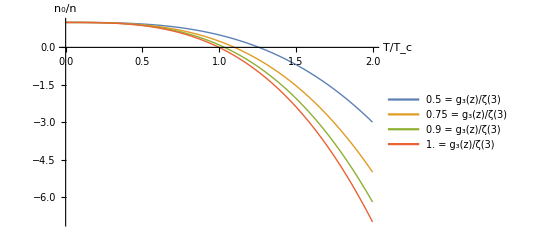

```mathematica
Clear[spinZeroBoseCondensationFig1]
spinZeroBoseCondensationFig1 = Module[
{a},
a = {0.5, 0.75, 0.9, 1.0} ;
Plot[Evaluate[(1 - # x^3) &/@ a], {x, 0, 2},
AxesLabel -> {T/Subscript[T, c] //fs, Subscript[n, 0]/n //fs},
PlotStyle->Thick,
PlotLegends -> Placed[ 
fs[Row[{#, Text[" = g_3(z)/ζ(3)" ]}] ]&
/@ a, {Left,Bottom}]
]
]
```

```mathematica
peeters`exportForLatex["spinZeroBoseCondensationFig1", spinZeroBoseCondensationFig1]
```

{spinZeroBoseCondensationFig1.eps,spinZeroBoseCondensationFig1pn.png}